## グローバル企業の憂鬱

```mathematica
(*　ver7用　*)
f001[r_(* 能力と語学力の相関 *)]:=Module[{score1,score2,all,a1,a2,new1,new2,
n=200,x=10,
m1=50(*能力平均*),
m2=50(*語学力平均*),s1=5,s2=5},
(*学生は仕事能力と語学力の二つを能力として持つ*)
all=RandomReal[
MultinormalDistribution[{m1,m2},{{s1^2,r*s1*s2},{r*s1*s2,s2^2}}],{n}];
(* 乱数の発生  ver7では RandomVariate　を使えない*)
a1=Sort[all,#1[[1]]>#2[[1]]&];(* 能力によるソート Print["a1= ",a1];*)

new1=Table[a1[[i]][[1]],{i,1,x}];(* 能力重視の選抜 *)
a2=Sort[all,#1[[2]]>#2[[2]]&];(* 語学力によるソート *)
new2=Table[a2[[i]][[1]],{i,1,x}];(* 語学力重視の選抜 *)
Print[{"能力重視した場合の生産性=",Mean[new1],"語学重視した場合の生産性=",Mean[new2],"p-value=",TTest[{new1,new2}]}];
ListPlot[a1,PlotRange->{{30,70},{30,70}}]
]
```

{能力重視した場合の生産性=,59.6295,語学重視した場合の生産性=,55.3769,p-value=,0.00270458}

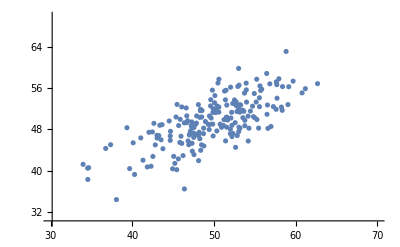

```mathematica
f001[0.7(* 能力と語学力の相関 *)]
```

## 二段階選抜モデル

```mathematica
f002[r_(* 生産力と語学力の相関 *)]:=Module[
{score1,score2,all,a1,a2,new1,new2,test1,test2,test3,test4,
n=1000,x1=20(* 第一段階選抜 *),x2=10(* 第二段階選抜 *),
m1=50(*生産力平均*),m2=50(*語学力平均*),s1=5,s2=5},
all=RandomVariate[
MultinormalDistribution[{m1,m2},{{s1^2,r*s1*s2},{r*s1*s2,s2^2}}],{n}];(* 乱数の発生 *)
a1=Sort[all,#1⟦2⟧>#2⟦2⟧&];(* 語学力でソート *)
test1=Table[a1⟦i⟧,{i,1,x1}];(* 第一段階選抜 *)
a2=Sort[test1,#1⟦1⟧>#2⟦1⟧&];(* 生産力でソート *)
test2=Table[a2⟦i⟧[[1]],{i,1,x2}];(* 第二段階選抜 *)

a1=Sort[all,#1⟦1⟧>#2⟦1⟧&];(* 生産力でソート *)
test3=Table[a1⟦i⟧,{i,1,x1}];(* 第一段階選抜 *)
a2=Sort[test3,#1⟦1⟧>#2⟦1⟧&];(* 語学でソート *)
test4=Table[a2⟦i⟧[[1]],{i,1,x2}];(* 第二段階選抜 *)
{"語学→生産力の生産性=",Mean[test2],"生産力→語学の生産性=",Mean[test4],"p-value=",TTest[{test2,test4}]}
]
```

```mathematica
f002[0.5(* 生産力と語学力の相関 *)]
```

{語学→生産力の生産性=,59.1235,生産力→語学の生産性=,64.4546,p-value=,0.0000708659}

```mathematica
{"語学→生産力の生産性=",59.822296004885196,"生産力→語学の生産性=",63.14849935100146}
```

```mathematica
問題．生産力と語学力の合計得点で選抜した場合の，生産能力の平均値を比較せよ
```

### 参考

#### 2次元正規分布の相関の違いを図示

```mathematica
ParallelTable[Plot3D[PDF[MultinormalDistribution[{-1,1},{{1,ρ 2},{ρ 2,4}}],{x,y}],{x,-3,3},{y,-6,6},PlotRange->All,MeshFunctions->{#3&},MeshShading->{None,Red,None,Yellow},PlotPoints->25],{ρ,{-.7,-0.4,0,0.3,0.5,0.8}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Covariance[MultinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},Σ]]
```

```mathematica
{{Subscript[σ, 11]^2,ρ Subscript[σ, 11] Subscript[σ, 22]},{ρ Subscript[σ, 11] Subscript[σ, 22],Subscript[σ, 22]^2}}
```

```mathematica
Plot3D[PDF[MultinormalDistribution[{50,50},{{6^2,6*0.5},{6*0.5,6^2}}],{x,y}],{x,30,70},{y,30,70},PlotPoints->25]
```

-Graphics3D-